# Regration Linéair

```mathematica
Clear["Global`*"]
```

```mathematica
Needs["ErrorBarPlots`"]
```

## Get current notebook directory

```mathematica
CurrentNotebookDirectory=NotebookDirectory[SelectedNotebook[]]
```

/Users/cafeplanck/Dropbox/Stop Teaching Calculating/Mathematics/---Statistics/

## Set Directory to current notebook directory

```mathematica
SetDirectory[CurrentNotebookDirectory]
```

/Users/cafeplanck/Dropbox/Stop Teaching Calculating/Mathematics/---Statistics

## Get Data

```mathematica
data=Import["mydata"];
```

### Les mesures des x

```mathematica
xList=data[[All,1]]
```

{2,3,5,6,8,12,13,15,18,20,22}

### Les incértitude de x

```mathematica
dxList=data[[All,2]]
```

{0.1,0.2,0.1,0.3,0.1,0.1,0.1,0.3,0.2,0.3,0.2}

### Les mesures des y

```mathematica
yList=data[[All,3]]
```

{4,5,8,7,9,11,13,21,20,23,25}

### Les incértitude de y

```mathematica
dyList=data[[All,4]]
```

{0.2,0.1,0.2,0.3,0.1,0.1,0.1,0.3,0.1,0.2,0.3}

```mathematica
xydyList=Table[{xList[[i]],yList[[i]],dyList[[i]]},{i,Length[xList]}]
```

{{2,4,0.2},{3,5,0.1},{5,8,0.2},{6,7,0.3},{8,9,0.1},{12,11,0.1},{13,13,0.1},{15,21,0.3},{18,20,0.1},{20,23,0.2},{22,25,0.3}}

```mathematica
xyList=Table[{xList[[i]],yList[[i]]},{i,Length[xList]}]
```

{{2,4},{3,5},{5,8},{6,7},{8,9},{12,11},{13,13},{15,21},{18,20},{20,23},{22,25}}

```mathematica
lm=LinearModelFit[xyList,x,x];
```

## Regration Linéair

```mathematica
b=lm["BestFitParameters"][[1]]
```

1.28123

```mathematica
db=lm["ParameterErrors"][[1]]/Sqrt[Length[xList]]//N
```

0.337568

```mathematica
m=lm["BestFitParameters"][[2]]
```

1.06376

```mathematica
dm=lm["ParameterErrors"][[2]]/Sqrt[Length[xList]]//N
```

0.0257939

### La ligne y=mx+b

```mathematica
lineFit=lm//Normal
```

1.28123+1.06376 x

```mathematica
p1:=ErrorListPlot[xydyList,Frame->True,FrameLabel->{"x","y"},PlotLabel->"y en fonction de x"]
```

```mathematica
p2:=Plot[lineFit,{x,0,25},Frame->True,PlotStyle->Red]
```

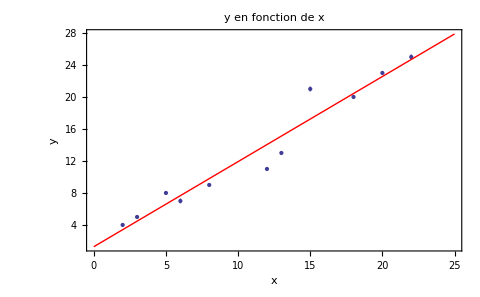

```mathematica
Show[p1,p2]
```